```mathematica
SetDirectory["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass"]
Needs["ErrorBarPlots`"]
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/ErrorBarLogPlots.m"]
Get["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/ProtonFluxAnn.m"]
```

/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass

InterpolatingFunction[…]

## AMS02-Experiment Error Bar Import

57

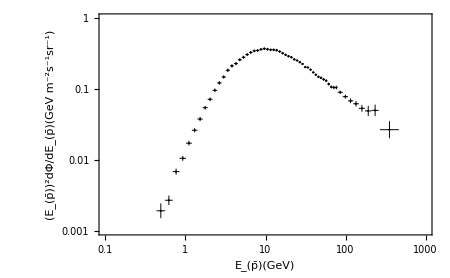

```mathematica
IErrorm = Import[ "/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IErrorm]
IError1m=Table[{IErrorm[[i,1]],IErrorm[[i,2]],(IErrorm[[i,4]]-IErrorm[[i,3]])/2,(IErrorm[[i,6]]-IErrorm[[i,5]])/2},{i,1,Length[IErrorm]}];
IError2m=IError1m/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlot1m=ErrorListLogLogPlot[IError2m,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

393

InterpolatingFunction[…]

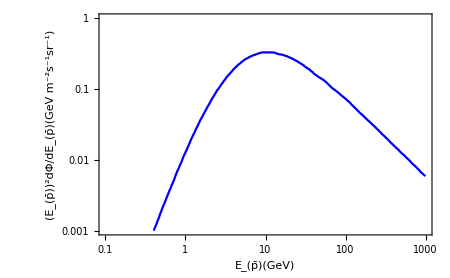

```mathematica
BG00m=Import["/Users/sinbi/desktop/AMS02.csv","CSV","HearderLines"->1];
BG01m=Table[BG00m[[i,All]],{i,7,399}];
Length[BG01m]
ifBG0m=Interpolation[BG01m]
BGPlotm=ListLogLogPlot[ifBG0m,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
GeV=1;
topm=173.0GeV;
taum=1.777GeV;
cm=1.275GeV;
bm=4.18 GeV;
qm=0.095 GeV;
```

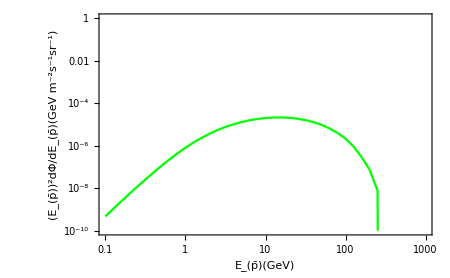

```mathematica
primaryτm="τ";
haloτm="NFW";
propagationτm="MED";
mDMτm=300GeV;
σvτm=10^-26;
Eγτ=10^lEγ;
Poτm=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτm, haloτm, propagationτm][mDMτm, σvτm,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDτm=ListLogLogPlot[Poτm,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

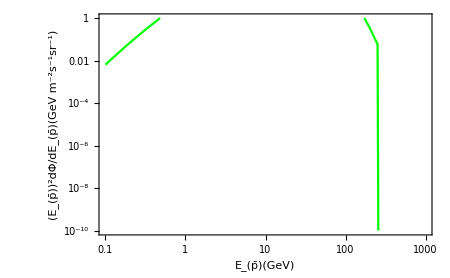

```mathematica
primarytm="t";
halotm="NFW";
propagationtm="MED";
mDMtm=300GeV;
σvtm=3×(topm/taum)^2×σvτm;
Eγτ=10^lEγ;
Potm=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarytm, halotm, propagationtm][mDMtm, σvtm,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDtm=ListLogLogPlot[Potm,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

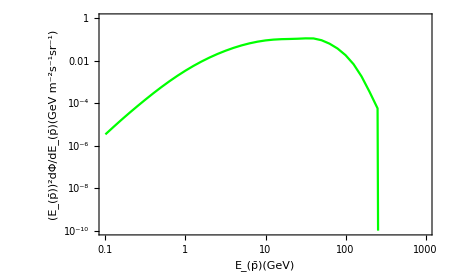

```mathematica
primarybm="b";
halobm="NFW";
propagationbm="MED";
mDMbm=300GeV;
σvbm=3×(bm/taum)^2×σvτm;
Eγτ=10^lEγ;
Pobm=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybm, halobm, propagationbm][mDMbm, σvbm,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDbm=ListLogLogPlot[Pobm,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

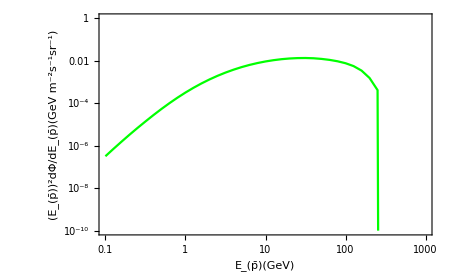

```mathematica
primarycm="c";
halocm="NFW";
propagationcm="MED";
mDMcm=300GeV;
σvcm=3×(cm/taum)^2×σvτm;
Eγτ=10^lEγ;
Pocm=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycm, halocm, propagationcm][mDMcm, σvcm,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDcm=ListLogLogPlot[Pocm,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

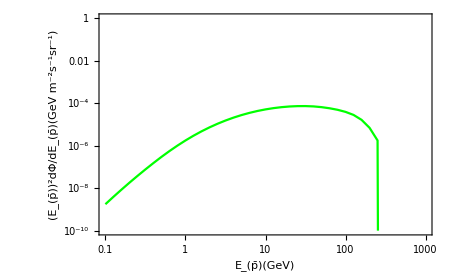

```mathematica
primaryqm="q";
haloqm="NFW";
propagationqm="MED";
mDMqm=300GeV;
σvqm=3×(qm/taum)^2×σvτm;
Eγτ=10^lEγ;
Poqm=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqm, haloqm, propagationqm][mDMqm, σvqm,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
PlotMEDqm=ListLogLogPlot[Poqm,PlotRange->{{10^-1,10^3},{10^-10,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

```mathematica
Length[Potm]
Length[Poτm]
Length[Pocm]
Length[Pobm]
Length[Poqm]
```

401

401

401

«2 more identical outputs»

```mathematica
ifPot1m=Table[{Poτm[[i,1]],(Potm[[i,2]]+Poτm[[i,2]]+Pocm[[i,2]]+Pobm[[i,2]]+Poqm[[i,2]])},{i,1,Length[Poτm]}];
Length[ifPot1m]
ifPot1fm=Interpolation[ifPot1m]
```

401

InterpolatingFunction[…]

```mathematica
ifPot2m=Table[{Poτm[[i,1]],(Poτm[[i,2]]+Pocm[[i,2]]+Pobm[[i,2]]+Poqm[[i,2]])},{i,1,Length[Poτm]}];
Length[ifPot2m]
ifPot2fm=Interpolation[ifPot2m]
```

401

InterpolatingFunction[…]

```mathematica
Sumdata01=Table[{x,ifBG0m[x]+ifPot1fm[x]},{x,0.18,10^2.99,0.1}]
Sumdata02=Table[{x,ifBG0m[x]+ifPot2fm[x]},{x,0.18,10^2.99,0.1}]
```

{{0.18,0.04787},{0.28,0.196788},{0.38,0.498762},{0.48,0.987305},{0.58,1.67033},{0.68,2.55171},{0.78,3.63396},{0.88,4.87352},9756,{976.58,0.00597456},{976.68,0.00597405},{976.78,0.00597354},{976.88,0.00597304},{976.98,0.00597254},{977.08,0.00597203},{977.18,0.00597153}}
 |  |  |  |

{{0.18,0.000137865},{0.28,0.000456329},{0.38,0.00113105},{0.48,0.00224022},{0.58,0.00383333},{0.68,0.00594851},{0.78,0.00868502},{0.88,0.0117769},9756,{976.58,0.00597456},{976.68,0.00597405},{976.78,0.00597354},{976.88,0.00597304},{976.98,0.00597254},{977.08,0.00597203},{977.18,0.00597153}}
 |  |  |  |

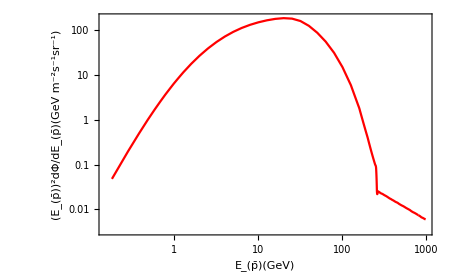

```mathematica
SumPlotifPot1m=ListLogLogPlot[Sumdata01,Joined->True,PlotStyle->Red,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

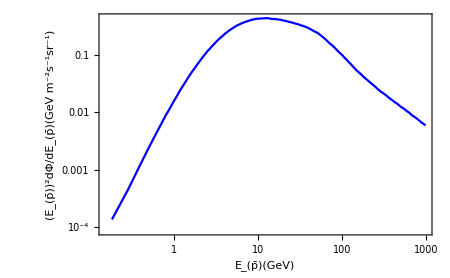

```mathematica
SumPlotifPot2m=ListLogLogPlot[Sumdata02,Joined->True,PlotStyle->Blue,Frame->True,Axes->False,ImageSize->450 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

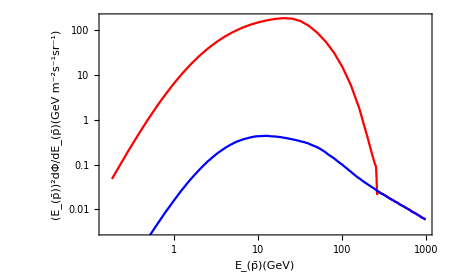

```mathematica
Show[SumPlotifPot1m,SumPlotifPot2m]
```

## χ^2- Fitting

```mathematica
SumY1m=Table[Sumdata01[IError1m[[i,1]]],{i,Length[IErrorm]}];
IErrorY1m=Flatten[Table[{IError1m[[i,2]]},{i,1,Length[IErrorm]}],1];
IErrorSize1m=Flatten[Table[{IError1m[[i,4]]},{i,1,Length[IErrorm]}],1];
chiSUM1m=((SumY1m-IErrorY1m)/IErrorSize1m)^2;
Sum[chiSUM1m[[i]],{i,1,Length[IErrorm]}];
SumY2m=Table[Sumdata02[IError1m[[i,1]]],{i,Length[IErrorm]}];
IErrorY2m=Flatten[Table[{IError1m[[i,2]]},{i,1,Length[IErrorm]}],1];
IErrorSize2m=Flatten[Table[{IError1m[[i,4]]},{i,1,Length[IErrorm]}],1];
chiSUM2m=((SumY2m-IErrorY2m)/IErrorSize2m)^2;
Sum[chiSUM2m[[i]],{i,1,Length[IErrorm]}];
```

## Mass-σv graph

```mathematica
ClearAll[σv2m,mDM02]
```

```mathematica
σv2m=10^lσv2m;
mDM02=10^lmDM02;
```

```mathematica
3×(bm/taum)^2
 3×(cm/taum)^2
```

16.5997

1.54442

```mathematica
Poτm2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryτm, haloτm, propagationτm][mDM02, σv2m,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pobm2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarybm, halobm, propagationbm][mDM02, 3×(bm/taum)^2×σv2m,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Pocm2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarycm, halocm, propagationcm][mDM02, 3×(cm/taum)^2×σv2m,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Poqm2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primaryqm, haloqm, propagationqm][mDM02, 3×(qm/taum)^2×σv2m,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
Potm2=Table[{10^lEγ,10^lEγ 10.^ ProtonFluxAnn[primarytm, halotm, propagationtm][mDM02, 3×(topm/taum)^2×σv2m,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}];
ifPot3m=Table[{Poτm2[[i,1]],(Potm2[[i,2]]+Poτm2[[i,2]]+Pocm2[[i,2]]+Pobm2[[i,2]]+Poqm2[[i,2]])},{i,1,Length[Poτm2]}];
Length[ifPot3m];
ifPot3fm=Interpolation[ifPot3m];
ifPot4m=Table[{Poτm2[[i,1]],(Poτm2[[i,2]]+Pocm2[[i,2]]+Pobm2[[i,2]]+Poqm2[[i,2]])},{i,1,Length[Poτm2]}];
Length[ifPot4m];
ifPot4fm=Interpolation[ifPot4m];
Sumdata03=Interpolation[Table[{x,ifBG0m[x]+ifPot3fm[x]},{x,0.18,10^2.99,0.1}]];
Sumdata04=Interpolation[Table[{x,ifBG0m[x]+ifPot4fm[x]},{x,0.18,10^2.99,0.1}]];
SumY3m=Table[Sumdata03[IError1m[[i,1]]],{i,Length[IErrorm]}];
chiSUMY03m=((SumY3m-IErrorY1m)/IErrorSize1m)^2;
FinalSum03=Sum[chiSUMY03m[[i]],{i,1,Length[IErrorm]}];
SumY4m=Table[Sumdata04[IError1m[[i,1]]],{i,Length[IErrorm]}];
chiSUMY04m=((SumY4m-IErrorY1m)/IErrorSize1m)^2;
FinalSum04=Sum[chiSUMY04m[[i]],{i,1,Length[IErrorm]}];
```

```mathematica
3*((topm/taum)^2+(bm/taum)^2+(cm/taum)^2+(qm/taum)^2)+1
3*((bm/taum)^2+(cm/taum)^2+(qm/taum)^2)+1
Log10[10^-28/28453.2]
Log10[10^-28/19.15]
```

28453.2

19.1527

-32.4541

-29.2822

```mathematica
contdata1=Flatten[Table[{mDM02,Log[10, (19.15*σv2m)], (19.15*σv2m),FinalSum04},{lmDM02,0.7,Log10[topm],0.02},{lσv2m,-29.282,-26.282,0.05}],1]
(* contdata1=Monitor[Flatten[Table[{mDM02,Log[10, (28522.3*σv2m)], (28522.3*σv2m),If[mDM02>173.21,FinalSum03]},{lmDM02,0.7,2.4,0.5},{lσv2m,-32.46,-29.46,0.5}],1],{mDM02,Log[10, (28522.3*σv2m)], (28522.3*σv2m),If[mDM02>173.21,FinalSum03]}] *)
Export["contour_AMS_RED_mass01.dat",contdata1,"Table"];
contdata2=Monitor[Flatten[Table[{mDM02,Log[10, (28453.2*σv2m)],(28453.2*σv2m),FinalSum03},{lmDM02,Log10[topm],2.4,0.02},{lσv2m,-32.454,-29.454,0.05}],1],{mDM02,Log[10, (28453.2*σv2m)],(28453.2*σv2m),FinalSum03}]
Export["contour_AMS_RED_mass02.dat",contdata2,"Table"];
contdata3=Join[contdata1,contdata2]
Export["contour_AMS_RED_mass03.dat",contdata3,"Table"]
```

{{5.01187,-27.9998,1.00039×10^-28,151.407},{5.01187,-27.9498,1.12245×10^-28,151.305},{5.01187,-27.8998,1.25941×10^-28,151.197},4691,{165.959,-25.0998,7.94637×10^-26,1899.35},{165.959,-25.0498,8.91597×10^-26,2450.24},{165.959,-24.9998,1.00039×10^-25,3155.79}}
 |  |  |  |

{{173.,-27.9999,1.0003×10^-28,152.447},{173.,-27.9499,1.12236×10^-28,152.447},{173.,-27.8999,1.25931×10^-28,152.447},{173.,-27.8499,1.41296×10^-28,152.447},{173.,-27.7999,1.58537×10^-28,152.446},{173.,-27.7499,1.77882×10^-28,152.446},{173.,-27.6999,1.99586×10^-28,152.446},{173.,-27.6499,2.2394×10^-28,152.446},{173.,-27.5999,2.51264×10^-28,152.446},{173.,-27.5499,2.81923×10^-28,152.446},{173.,-27.4999,3.16323×10^-28,152.446},{173.,-27.4499,3.54921×10^-28,152.445},{173.,-27.3999,3.98227×10^-28,152.445},{173.,-27.3499,4.46818×10^-28,152.445},{173.,-27.2999,5.01339×10^-28,152.444},{173.,-27.2499,5.62511×10^-28,152.444},{173.,-27.1999,6.31148×10^-28,152.444},{173.,-27.1499,7.0816×10^-28,152.443},{173.,-27.0999,7.94568×10^-28,152.443},{173.,-27.0499,8.9152×10^-28,152.442},{173.,-26.9999,1.0003×10^-27,152.442},{173.,-26.9499,1.12236×10^-27,152.441},{173.,-26.8999,1.25931×10^-27,152.44},{173.,-26.8499,1.41296×10^-27,152.439},{173.,-26.7999,1.58537×10^-27,152.438},{173.,-26.7499,1.77882×10^-27,152.437},{173.,-26.6999,1.99586×10^-27,152.436},{173.,-26.6499,2.2394×10^-27,152.434},{173.,-26.5999,2.51264×10^-27,152.433},{173.,-26.5499,2.81923×10^-27,152.431},{173.,-26.4999,3.16323×10^-27,152.429},{173.,-26.4499,3.54921×10^-27,152.427},{173.,-26.3999,3.98227×10^-27,152.424},{173.,-26.3499,4.46818×10^-27,152.421},{173.,-26.2999,5.01339×10^-27,152.418},{173.,-26.2499,5.62511×10^-27,152.415},{173.,-26.1999,6.31148×10^-27,152.411},{173.,-26.1499,7.0816×10^-27,152.406},{173.,-26.0999,7.94568×10^-27,152.401},{173.,-26.0499,8.9152×10^-27,152.395},{173.,-25.9999,1.0003×10^-26,152.389},{173.,-25.9499,1.12236×10^-26,152.382},{173.,-25.8999,1.25931×10^-26,152.374},{173.,-25.8499,1.41296×10^-26,152.365},{173.,-25.7999,1.58537×10^-26,152.355},{173.,-25.7499,1.77882×10^-26,152.344},{173.,-25.6999,1.99586×10^-26,152.331},{173.,-25.6499,2.2394×10^-26,152.317},{173.,-25.5999,2.51264×10^-26,152.301},{173.,-25.5499,2.81923×10^-26,152.283},{173.,-25.4999,3.16323×10^-26,152.263},{173.,-25.4499,3.54921×10^-26,152.241},{173.,-25.3999,3.98227×10^-26,152.216},{173.,-25.3499,4.46818×10^-26,152.187},{173.,-25.2999,5.01339×10^-26,152.156},{173.,-25.2499,5.62511×10^-26,152.12},{173.,-25.1999,6.31148×10^-26,152.08},{173.,-25.1499,7.0816×10^-26,152.035},{173.,-25.0999,7.94568×10^-26,151.985},{173.,-25.0499,8.9152×10^-26,151.929},{173.,-24.9999,1.0003×10^-25,151.866},{181.153,-27.9999,1.0003×10^-28,151.666},{181.153,-27.9499,1.12236×10^-28,151.571},{181.153,-27.8999,1.25931×10^-28,151.464},{181.153,-27.8499,1.41296×10^-28,151.344},{181.153,-27.7999,1.58537×10^-28,151.21},{181.153,-27.7499,1.77882×10^-28,151.06},{181.153,-27.6999,1.99586×10^-28,150.891},{181.153,-27.6499,2.2394×10^-28,150.703},{181.153,-27.5999,2.51264×10^-28,150.491},{181.153,-27.5499,2.81923×10^-28,150.254},{181.153,-27.4999,3.16323×10^-28,149.988},{181.153,-27.4499,3.54921×10^-28,149.691},{181.153,-27.3999,3.98227×10^-28,149.358},{181.153,-27.3499,4.46818×10^-28,148.985},{181.153,-27.2999,5.01339×10^-28,148.567},{181.153,-27.2499,5.62511×10^-28,148.1},{181.153,-27.1999,6.31148×10^-28,147.578},{181.153,-27.1499,7.0816×10^-28,146.994},{181.153,-27.0999,7.94568×10^-28,146.341},{181.153,-27.0499,8.9152×10^-28,145.612},{181.153,-26.9999,1.0003×10^-27,144.799},{181.153,-26.9499,1.12236×10^-27,143.891},{181.153,-26.8999,1.25931×10^-27,142.879},{181.153,-26.8499,1.41296×10^-27,141.752},{181.153,-26.7999,1.58537×10^-27,140.498},{181.153,-26.7499,1.77882×10^-27,139.105},{181.153,-26.6999,1.99586×10^-27,137.557},{181.153,-26.6499,2.2394×10^-27,135.842},{181.153,-26.5999,2.51264×10^-27,133.944},{181.153,-26.5499,2.81923×10^-27,131.848},{181.153,-26.4999,3.16323×10^-27,129.538},{181.153,-26.4499,3.54921×10^-27,126.998},{181.153,-26.3999,3.98227×10^-27,124.215},{181.153,-26.3499,4.46818×10^-27,121.175},{181.153,-26.2999,5.01339×10^-27,117.87},{181.153,-26.2499,5.62511×10^-27,114.293},{181.153,-26.1999,6.31148×10^-27,110.446},{181.153,-26.1499,7.0816×10^-27,106.34},{181.153,-26.0999,7.94568×10^-27,101.995},{181.153,-26.0499,8.9152×10^-27,97.4531},{181.153,-25.9999,1.0003×10^-26,92.7755},{181.153,-25.9499,1.12236×10^-26,88.0507},{181.153,-25.8999,1.25931×10^-26,83.4129},{181.153,-25.8499,1.41296×10^-26,79.0428},{181.153,-25.7999,1.58537×10^-26,75.1891},{181.153,-25.7499,1.77882×10^-26,72.1864},{181.153,-25.6999,1.99586×10^-26,70.4808},{181.153,-25.6499,2.2394×10^-26,70.6611},{181.153,-25.5999,2.51264×10^-26,73.4998},{181.153,-25.5499,2.81923×10^-26,80.0038},{181.153,-25.4999,3.16323×10^-26,91.4797},{181.153,-25.4499,3.54921×10^-26,109.616},{181.153,-25.3999,3.98227×10^-26,136.587},{181.153,-25.3499,4.46818×10^-26,175.187},{181.153,-25.2999,5.01339×10^-26,228.991},{181.153,-25.2499,5.62511×10^-26,302.573},{181.153,-25.1999,6.31148×10^-26,401.768},{181.153,-25.1499,7.0816×10^-26,534.007},{181.153,-25.0999,7.94568×10^-26,708.747},{181.153,-25.0499,8.9152×10^-26,937.996},{181.153,-24.9999,1.0003×10^-25,1237.},{189.691,-27.9999,1.0003×10^-28,151.718},{189.691,-27.9499,1.12236×10^-28,151.629},{189.691,-27.8999,1.25931×10^-28,151.53},{189.691,-27.8499,1.41296×10^-28,151.418},{189.691,-27.7999,1.58537×10^-28,151.293},{189.691,-27.7499,1.77882×10^-28,151.153},{189.691,-27.6999,1.99586×10^-28,150.996},{189.691,-27.6499,2.2394×10^-28,150.819},{189.691,-27.5999,2.51264×10^-28,150.622},{189.691,-27.5499,2.81923×10^-28,150.401},{189.691,-27.4999,3.16323×10^-28,150.153},{189.691,-27.4499,3.54921×10^-28,149.875},{189.691,-27.3999,3.98227×10^-28,149.564},{189.691,-27.3499,4.46818×10^-28,149.216},{189.691,-27.2999,5.01339×10^-28,148.827},{189.691,-27.2499,5.62511×10^-28,148.391},{189.691,-27.1999,6.31148×10^-28,147.903},{189.691,-27.1499,7.0816×10^-28,147.358},{189.691,-27.0999,7.94568×10^-28,146.749},{189.691,-27.0499,8.9152×10^-28,146.068},{189.691,-26.9999,1.0003×10^-27,145.309},{189.691,-26.9499,1.12236×10^-27,144.461},{189.691,-26.8999,1.25931×10^-27,143.516},{189.691,-26.8499,1.41296×10^-27,142.463},{189.691,-26.7999,1.58537×10^-27,141.292},{189.691,-26.7499,1.77882×10^-27,139.99},{189.691,-26.6999,1.99586×10^-27,138.544},{189.691,-26.6499,2.2394×10^-27,136.94},{189.691,-26.5999,2.51264×10^-27,135.166},{189.691,-26.5499,2.81923×10^-27,133.205},{189.691,-26.4999,3.16323×10^-27,131.044},{189.691,-26.4499,3.54921×10^-27,128.666},{189.691,-26.3999,3.98227×10^-27,126.06},{189.691,-26.3499,4.46818×10^-27,123.212},{189.691,-26.2999,5.01339×10^-27,120.113},{189.691,-26.2499,5.62511×10^-27,116.756},{189.691,-26.1999,6.31148×10^-27,113.143},{189.691,-26.1499,7.0816×10^-27,109.281},{189.691,-26.0999,7.94568×10^-27,105.189},{189.691,-26.0499,8.9152×10^-27,100.902},{189.691,-25.9999,1.0003×10^-26,96.4754},{189.691,-25.9499,1.12236×10^-26,91.9909},{189.691,-25.8999,1.25931×10^-26,87.5665},{189.691,-25.8499,1.41296×10^-26,83.3667},{189.691,-25.7999,1.58537×10^-26,79.6169},{189.691,-25.7499,1.77882×10^-26,76.621},{189.691,-25.6999,1.99586×10^-26,74.7849},{189.691,-25.6499,2.2394×10^-26,74.645},{189.691,-25.5999,2.51264×10^-26,76.9054},{189.691,-25.5499,2.81923×10^-26,82.485},{189.691,-25.4999,3.16323×10^-26,92.5768},{189.691,-25.4499,3.54921×10^-26,108.723},{189.691,-25.3999,3.98227×10^-26,132.912},{189.691,-25.3499,4.46818×10^-26,167.697},{189.691,-25.2999,5.01339×10^-26,216.35},{189.691,-25.2499,5.62511×10^-26,282.986},{189.691,-25.1999,6.31148×10^-26,373.018},{189.691,-25.1499,7.0816×10^-26,493.448},{189.691,-25.0999,7.94568×10^-26,652.593},{189.691,-25.0499,8.9152×10^-26,861.591},{189.691,-24.9999,1.0003×10^-25,1134.4},{198.631,-27.9999,1.0003×10^-28,151.765},{198.631,-27.9499,1.12236×10^-28,151.682},{198.631,-27.8999,1.25931×10^-28,151.589},{198.631,-27.8499,1.41296×10^-28,151.485},{198.631,-27.7999,1.58537×10^-28,151.368},{198.631,-27.7499,1.77882×10^-28,151.237},{198.631,-27.6999,1.99586×10^-28,151.09},{198.631,-27.6499,2.2394×10^-28,150.925},{198.631,-27.5999,2.51264×10^-28,150.74},{198.631,-27.5499,2.81923×10^-28,150.534},{198.631,-27.4999,3.16323×10^-28,150.302},{198.631,-27.4499,3.54921×10^-28,150.042},{198.631,-27.3999,3.98227×10^-28,149.751},{198.631,-27.3499,4.46818×10^-28,149.426},{198.631,-27.2999,5.01339×10^-28,149.062},{198.631,-27.2499,5.62511×10^-28,148.654},{198.631,-27.1999,6.31148×10^-28,148.198},{198.631,-27.1499,7.0816×10^-28,147.688},{198.631,-27.0999,7.94568×10^-28,147.119},{198.631,-27.0499,8.9152×10^-28,146.482},{198.631,-26.9999,1.0003×10^-27,145.772},{198.631,-26.9499,1.12236×10^-27,144.979},{198.631,-26.8999,1.25931×10^-27,144.096},{198.631,-26.8499,1.41296×10^-27,143.112},{198.631,-26.7999,1.58537×10^-27,142.016},{198.631,-26.7499,1.77882×10^-27,140.799},{198.631,-26.6999,1.99586×10^-27,139.447},{198.631,-26.6499,2.2394×10^-27,137.948},{198.631,-26.5999,2.51264×10^-27,136.289},{198.631,-26.5499,2.81923×10^-27,134.456},{198.631,-26.4999,3.16323×10^-27,132.436},{198.631,-26.4499,3.54921×10^-27,130.214},{198.631,-26.3999,3.98227×10^-27,127.778},{198.631,-26.3499,4.46818×10^-27,125.116},{198.631,-26.2999,5.01339×10^-27,122.22},{198.631,-26.2499,5.62511×10^-27,119.083},{198.631,-26.1999,6.31148×10^-27,115.708},{198.631,-26.1499,7.0816×10^-27,112.1},{198.631,-26.0999,7.94568×10^-27,108.278},{198.631,-26.0499,8.9152×10^-27,104.276},{198.631,-25.9999,1.0003×10^-26,100.144},{198.631,-25.9499,1.12236×10^-26,95.9601},{198.631,-25.8999,1.25931×10^-26,91.8349},{198.631,-25.8499,1.41296×10^-26,87.923},{198.631,-25.7999,1.58537×10^-26,84.4357},{198.631,-25.7499,1.77882×10^-26,81.6586},{198.631,-25.6999,1.99586×10^-26,79.9722},{198.631,-25.6499,2.2394×10^-26,79.88},{198.631,-25.5999,2.51264×10^-26,82.0423},{198.631,-25.5499,2.81923×10^-26,87.3211},{198.631,-25.4999,3.16323×10^-26,96.8351},{198.631,-25.4499,3.54921×10^-26,112.031},{198.631,-25.3999,3.98227×10^-26,134.773},{198.631,-25.3499,4.46818×10^-26,167.455},{198.631,-25.2999,5.01339×10^-26,213.145},{198.631,-25.2499,5.62511×10^-26,275.767},{198.631,-25.1999,6.31148×10^-26,360.326},{198.631,-25.1499,7.0816×10^-26,473.202},{198.631,-25.0999,7.94568×10^-26,622.509},{198.631,-25.0499,8.9152×10^-26,818.56},{198.631,-24.9999,1.0003×10^-25,1074.44},{207.992,-27.9999,1.0003×10^-28,151.805},{207.992,-27.9499,1.12236×10^-28,151.727},{207.992,-27.8999,1.25931×10^-28,151.639},{207.992,-27.8499,1.41296×10^-28,151.541},{207.992,-27.7999,1.58537×10^-28,151.431},{207.992,-27.7499,1.77882×10^-28,151.307},{207.992,-27.6999,1.99586×10^-28,151.168},{207.992,-27.6499,2.2394×10^-28,151.013},{207.992,-27.5999,2.51264×10^-28,150.839},{207.992,-27.5499,2.81923×10^-28,150.644},{207.992,-27.4999,3.16323×10^-28,150.426},{207.992,-27.4499,3.54921×10^-28,150.181},{207.992,-27.3999,3.98227×10^-28,149.907},{207.992,-27.3499,4.46818×10^-28,149.601},{207.992,-27.2999,5.01339×10^-28,149.258},{207.992,-27.2499,5.62511×10^-28,148.874},{207.992,-27.1999,6.31148×10^-28,148.444},{207.992,-27.1499,7.0816×10^-28,147.964},{207.992,-27.0999,7.94568×10^-28,147.425},{207.992,-27.0499,8.9152×10^-28,146.827},{207.992,-26.9999,1.0003×10^-27,146.158},{207.992,-26.9499,1.12236×10^-27,145.411},{207.992,-26.8999,1.25931×10^-27,144.579},{207.992,-26.8499,1.41296×10^-27,143.651},{207.992,-26.7999,1.58537×10^-27,142.619},{207.992,-26.7499,1.77882×10^-27,141.472},{207.992,-26.6999,1.99586×10^-27,140.198},{207.992,-26.6499,2.2394×10^-27,138.786},{207.992,-26.5999,2.51264×10^-27,137.222},{207.992,-26.5499,2.81923×10^-27,135.495},{207.992,-26.4999,3.16323×10^-27,133.59},{207.992,-26.4499,3.54921×10^-27,131.496},{207.992,-26.3999,3.98227×10^-27,129.199},{207.992,-26.3499,4.46818×10^-27,126.689},{207.992,-26.2999,5.01339×10^-27,123.958},{207.992,-26.2499,5.62511×10^-27,121.001},{207.992,-26.1999,6.31148×10^-27,117.816},{207.992,-26.1499,7.0816×10^-27,114.413},{207.992,-26.0999,7.94568×10^-27,110.806},{207.992,-26.0499,8.9152×10^-27,107.028},{207.992,-25.9999,1.0003×10^-26,103.126},{207.992,-25.9499,1.12236×10^-26,99.1721},{207.992,-25.8999,1.25931×10^-26,95.2705},{207.992,-25.8499,1.41296×10^-26,91.5657},{207.992,-25.7999,1.58537×10^-26,88.2561},{207.992,-25.7499,1.77882×10^-26,85.6091},{207.992,-25.6999,1.99586×10^-26,83.9819},{207.992,-25.6499,2.2394×10^-26,83.8464},{207.992,-25.5999,2.51264×10^-26,85.8223},{207.992,-25.5499,2.81923×10^-26,90.7184},{207.992,-25.4999,3.16323×10^-26,99.5845},{207.992,-25.4499,3.54921×10^-26,113.778},{207.992,-25.3999,3.98227×10^-26,135.049},{207.992,-25.3499,4.46818×10^-26,165.645},{207.992,-25.2999,5.01339×10^-26,208.446},{207.992,-25.2499,5.62511×10^-26,267.135},{207.992,-25.1999,6.31148×10^-26,346.411},{207.992,-25.1499,7.0816×10^-26,452.16},{207.992,-25.0999,7.94568×10^-26,592.312},{207.992,-25.0499,8.9152×10^-26,776.239},{207.992,-24.9999,1.0003×10^-25,1016.34},{217.794,-27.9999,1.0003×10^-28,151.841},{217.794,-27.9499,1.12236×10^-28,151.767},{217.794,-27.8999,1.25931×10^-28,151.685},{217.794,-27.8499,1.41296×10^-28,151.592},{217.794,-27.7999,1.58537×10^-28,151.488},{217.794,-27.7499,1.77882×10^-28,151.371},{217.794,-27.6999,1.99586×10^-28,151.24},{217.794,-27.6499,2.2394×10^-28,151.094},{217.794,-27.5999,2.51264×10^-28,150.93},{217.794,-27.5499,2.81923×10^-28,150.746},{217.794,-27.4999,3.16323×10^-28,150.54},{217.794,-27.4499,3.54921×10^-28,150.309},{217.794,-27.3999,3.98227×10^-28,150.051},{217.794,-27.3499,4.46818×10^-28,149.761},{217.794,-27.2999,5.01339×10^-28,149.438},{217.794,-27.2499,5.62511×10^-28,149.075},{217.794,-27.1999,6.31148×10^-28,148.67},{217.794,-27.1499,7.0816×10^-28,148.217},{217.794,-27.0999,7.94568×10^-28,147.71},{217.794,-27.0499,8.9152×10^-28,147.145},{217.794,-26.9999,1.0003×10^-27,146.513},{217.794,-26.9499,1.12236×10^-27,145.809},{217.794,-26.8999,1.25931×10^-27,145.023},{217.794,-26.8499,1.41296×10^-27,144.148},{217.794,-26.7999,1.58537×10^-27,143.175},{217.794,-26.7499,1.77882×10^-27,142.093},{217.794,-26.6999,1.99586×10^-27,140.891},{217.794,-26.6499,2.2394×10^-27,139.558},{217.794,-26.5999,2.51264×10^-27,138.084},{217.794,-26.5499,2.81923×10^-27,136.455},{217.794,-26.4999,3.16323×10^-27,134.659},{217.794,-26.4499,3.54921×10^-27,132.684},{217.794,-26.3999,3.98227×10^-27,130.518},{217.794,-26.3499,4.46818×10^-27,128.152},{217.794,-26.2999,5.01339×10^-27,125.578},{217.794,-26.2499,5.62511×10^-27,122.791},{217.794,-26.1999,6.31148×10^-27,119.791},{217.794,-26.1499,7.0816×10^-27,116.585},{217.794,-26.0999,7.94568×10^-27,113.189},{217.794,-26.0499,8.9152×10^-27,109.633},{217.794,-25.9999,1.0003×10^-26,105.963},{217.794,-25.9499,1.12236×10^-26,102.246},{217.794,-25.8999,1.25931×10^-26,98.5832},{217.794,-25.8499,1.41296×10^-26,95.1106},{217.794,-25.7999,1.58537×10^-26,92.0169},{217.794,-25.7499,1.77882×10^-26,89.5561},{217.794,-25.6999,1.99586×10^-26,88.0672},{217.794,-25.6499,2.2394×10^-26,87.998},{217.794,-25.5999,2.51264×10^-26,89.9365},{217.794,-25.5499,2.81923×10^-26,94.6496},{217.794,-25.4999,3.16323×10^-26,103.133},{217.794,-25.4499,3.54921×10^-26,116.663},{217.794,-25.3999,3.98227×10^-26,136.932},{217.794,-25.3499,4.46818×10^-26,166.037},{217.794,-25.2999,5.01339×10^-26,206.72},{217.794,-25.2499,5.62511×10^-26,262.471},{217.794,-25.1999,6.31148×10^-26,337.746},{217.794,-25.1499,7.0816×10^-26,438.219},{217.794,-25.0999,7.94568×10^-26,571.114},{217.794,-25.0499,8.9152×10^-26,745.605},{217.794,-24.9999,1.0003×10^-25,973.34},{228.058,-27.9999,1.0003×10^-28,151.873},{228.058,-27.9499,1.12236×10^-28,151.803},{228.058,-27.8999,1.25931×10^-28,151.725},{228.058,-27.8499,1.41296×10^-28,151.637},{228.058,-27.7999,1.58537×10^-28,151.539},{228.058,-27.7499,1.77882×10^-28,151.428},{228.058,-27.6999,1.99586×10^-28,151.304},{228.058,-27.6499,2.2394×10^-28,151.166},{228.058,-27.5999,2.51264×10^-28,151.01},{228.058,-27.5499,2.81923×10^-28,150.836},{228.058,-27.4999,3.16323×10^-28,150.641},{228.058,-27.4499,3.54921×10^-28,150.422},{228.058,-27.3999,3.98227×10^-28,150.177},{228.058,-27.3499,4.46818×10^-28,149.903},{228.058,-27.2999,5.01339×10^-28,149.597},{228.058,-27.2499,5.62511×10^-28,149.253},{228.058,-27.1999,6.31148×10^-28,148.869},{228.058,-27.1499,7.0816×10^-28,148.44},{228.058,-27.0999,7.94568×10^-28,147.961},{228.058,-27.0499,8.9152×10^-28,147.425},{228.058,-26.9999,1.0003×10^-27,146.826},{228.058,-26.9499,1.12236×10^-27,146.159},{228.058,-26.8999,1.25931×10^-27,145.415},{228.058,-26.8499,1.41296×10^-27,144.586},{228.058,-26.7999,1.58537×10^-27,143.664},{228.058,-26.7499,1.77882×10^-27,142.639},{228.058,-26.6999,1.99586×10^-27,141.5},{228.058,-26.6499,2.2394×10^-27,140.238},{228.058,-26.5999,2.51264×10^-27,138.841},{228.058,-26.5499,2.81923×10^-27,137.297},{228.058,-26.4999,3.16323×10^-27,135.595},{228.058,-26.4499,3.54921×10^-27,133.725},{228.058,-26.3999,3.98227×10^-27,131.672},{228.058,-26.3499,4.46818×10^-27,129.43},{228.058,-26.2999,5.01339×10^-27,126.99},{228.058,-26.2499,5.62511×10^-27,124.347},{228.058,-26.1999,6.31148×10^-27,121.503},{228.058,-26.1499,7.0816×10^-27,118.463},{228.058,-26.0999,7.94568×10^-27,115.242},{228.058,-26.0499,8.9152×10^-27,111.868},{228.058,-25.9999,1.0003×10^-26,108.384},{228.058,-25.9499,1.12236×10^-26,104.855},{228.058,-25.8999,1.25931×10^-26,101.374},{228.058,-25.8499,1.41296×10^-26,98.0703},{228.058,-25.7999,1.58537×10^-26,95.1217},{228.058,-25.7499,1.77882×10^-26,92.7679},{228.058,-25.6999,1.99586×10^-26,91.3285},{228.058,-25.6499,2.2394×10^-26,91.2262},{228.058,-25.5999,2.51264×10^-26,93.016},{228.058,-25.5499,2.81923×10^-26,97.4218},{228.058,-25.4999,3.16323×10^-26,105.384},{228.058,-25.4499,3.54921×10^-26,118.117},{228.058,-25.3999,3.98227×10^-26,137.188},{228.058,-25.3499,4.46818×10^-26,164.608},{228.058,-25.2999,5.01339×10^-26,202.957},{228.058,-25.2499,5.62511×10^-26,255.529},{228.058,-25.1999,6.31148×10^-26,326.533},{228.058,-25.1499,7.0816×10^-26,421.329},{228.058,-25.0999,7.94568×10^-26,546.736},{228.058,-25.0499,8.9152×10^-26,711.422},{228.058,-24.9999,1.0003×10^-25,926.387},{238.806,-27.9999,1.0003×10^-28,151.903},{238.806,-27.9499,1.12236×10^-28,151.837},{238.806,-27.8999,1.25931×10^-28,151.762},{238.806,-27.8499,1.41296×10^-28,151.679},{238.806,-27.7999,1.58537×10^-28,151.586},{238.806,-27.7499,1.77882×10^-28,151.481},{238.806,-27.6999,1.99586×10^-28,151.364},{238.806,-27.6499,2.2394×10^-28,151.232},{238.806,-27.5999,2.51264×10^-28,151.085},{238.806,-27.5499,2.81923×10^-28,150.92},{238.806,-27.4999,3.16323×10^-28,150.735},{238.806,-27.4499,3.54921×10^-28,150.527},{238.806,-27.3999,3.98227×10^-28,150.295},{238.806,-27.3499,4.46818×10^-28,150.035},{238.806,-27.2999,5.01339×10^-28,149.745},{238.806,-27.2499,5.62511×10^-28,149.419},{238.806,-27.1999,6.31148×10^-28,149.055},{238.806,-27.1499,7.0816×10^-28,148.648},{238.806,-27.0999,7.94568×10^-28,148.193},{238.806,-27.0499,8.9152×10^-28,147.685},{238.806,-26.9999,1.0003×10^-27,147.118},{238.806,-26.9499,1.12236×10^-27,146.486},{238.806,-26.8999,1.25931×10^-27,145.78},{238.806,-26.8499,1.41296×10^-27,144.994},{238.806,-26.7999,1.58537×10^-27,144.12},{238.806,-26.7499,1.77882×10^-27,143.148},{238.806,-26.6999,1.99586×10^-27,142.069},{238.806,-26.6499,2.2394×10^-27,140.872},{238.806,-26.5999,2.51264×10^-27,139.547},{238.806,-26.5499,2.81923×10^-27,138.084},{238.806,-26.4999,3.16323×10^-27,136.47},{238.806,-26.4499,3.54921×10^-27,134.696},{238.806,-26.3999,3.98227×10^-27,132.75},{238.806,-26.3499,4.46818×10^-27,130.624},{238.806,-26.2999,5.01339×10^-27,128.311},{238.806,-26.2499,5.62511×10^-27,125.806},{238.806,-26.1999,6.31148×10^-27,123.109},{238.806,-26.1499,7.0816×10^-27,120.227},{238.806,-26.0999,7.94568×10^-27,117.173},{238.806,-26.0499,8.9152×10^-27,113.974},{238.806,-25.9999,1.0003×10^-26,110.671},{238.806,-25.9499,1.12236×10^-26,107.325},{238.806,-25.8999,1.25931×10^-26,104.025},{238.806,-25.8499,1.41296×10^-26,100.892},{238.806,-25.7999,1.58537×10^-26,98.0966},{238.806,-25.7499,1.77882×10^-26,95.8646},{238.806,-25.6999,1.99586×10^-26,94.4995},{238.806,-25.6499,2.2394×10^-26,94.402},{238.806,-25.5999,2.51264×10^-26,96.0982},{238.806,-25.5499,2.81923×10^-26,100.274},{238.806,-25.4999,3.16323×10^-26,107.822},{238.806,-25.4499,3.54921×10^-26,119.893},{238.806,-25.3999,3.98227×10^-26,137.972},{238.806,-25.3499,4.46818×10^-26,163.967},{238.806,-25.2999,5.01339×10^-26,200.321},{238.806,-25.2499,5.62511×10^-26,250.161},{238.806,-25.1999,6.31148×10^-26,317.474},{238.806,-25.1499,7.0816×10^-26,407.343},{238.806,-25.0999,7.94568×10^-26,526.234},{238.806,-25.0499,8.9152×10^-26,682.361},{238.806,-24.9999,1.0003×10^-25,886.155},{250.061,-27.9999,1.0003×10^-28,151.93},{250.061,-27.9499,1.12236×10^-28,151.867},{250.061,-27.8999,1.25931×10^-28,151.796},{250.061,-27.8499,1.41296×10^-28,151.717},{250.061,-27.7999,1.58537×10^-28,151.628},{250.061,-27.7499,1.77882×10^-28,151.529},{250.061,-27.6999,1.99586×10^-28,151.417},{250.061,-27.6499,2.2394×10^-28,151.292},{250.061,-27.5999,2.51264×10^-28,151.152},{250.061,-27.5499,2.81923×10^-28,150.995},{250.061,-27.4999,3.16323×10^-28,150.819},{250.061,-27.4499,3.54921×10^-28,150.622},{250.061,-27.3999,3.98227×10^-28,150.401},{250.061,-27.3499,4.46818×10^-28,150.155},{250.061,-27.2999,5.01339×10^-28,149.878},{250.061,-27.2499,5.62511×10^-28,149.569},{250.061,-27.1999,6.31148×10^-28,149.223},{250.061,-27.1499,7.0816×10^-28,148.836},{250.061,-27.0999,7.94568×10^-28,148.403},{250.061,-27.0499,8.9152×10^-28,147.92},{250.061,-26.9999,1.0003×10^-27,147.381},{250.061,-26.9499,1.12236×10^-27,146.779},{250.061,-26.8999,1.25931×10^-27,146.109},{250.061,-26.8499,1.41296×10^-27,145.361},{250.061,-26.7999,1.58537×10^-27,144.53},{250.061,-26.7499,1.77882×10^-27,143.605},{250.061,-26.6999,1.99586×10^-27,142.579},{250.061,-26.6499,2.2394×10^-27,141.44},{250.061,-26.5999,2.51264×10^-27,140.18},{250.061,-26.5499,2.81923×10^-27,138.788},{250.061,-26.4999,3.16323×10^-27,137.253},{250.061,-26.4499,3.54921×10^-27,135.564},{250.061,-26.3999,3.98227×10^-27,133.713},{250.061,-26.3499,4.46818×10^-27,131.689},{250.061,-26.2999,5.01339×10^-27,129.487},{250.061,-26.2499,5.62511×10^-27,127.101},{250.061,-26.1999,6.31148×10^-27,124.532},{250.061,-26.1499,7.0816×10^-27,121.784},{250.061,-26.0999,7.94568×10^-27,118.874},{250.061,-26.0499,8.9152×10^-27,115.822},{250.061,-25.9999,1.0003×10^-26,112.669},{250.061,-25.9499,1.12236×10^-26,109.471},{250.061,-25.8999,1.25931×10^-26,106.312},{250.061,-25.8499,1.41296×10^-26,103.307},{250.061,-25.7999,1.58537×10^-26,100.615},{250.061,-25.7499,1.77882×10^-26,98.4502},{250.061,-25.6999,1.99586×10^-26,97.0983},{250.061,-25.6499,2.2394×10^-26,96.9373},{250.061,-25.5999,2.51264×10^-26,98.4636},{250.061,-25.5499,2.81923×10^-26,102.325},{250.061,-25.4999,3.16323×10^-26,109.363},{250.061,-25.4499,3.54921×10^-26,120.666},{250.061,-25.3999,3.98227×10^-26,137.636},{250.061,-25.3499,4.46818×10^-26,162.074},{250.061,-25.2999,5.01339×10^-26,196.29},{250.061,-25.2499,5.62511×10^-26,243.236},{250.061,-25.1999,6.31148×10^-26,306.681},{250.061,-25.1499,7.0816×10^-26,391.426},{250.061,-25.0999,7.94568×10^-26,503.582},{250.061,-25.0499,8.9152×10^-26,650.913},{250.061,-24.9999,1.0003×10^-25,843.274}}

{{5.01187,-27.9998,1.00039×10^-28,151.407},{5.01187,-27.9498,1.12245×10^-28,151.305},{5.01187,-27.8998,1.25941×10^-28,151.197},5240,{250.061,-25.0999,7.94568×10^-26,503.582},{250.061,-25.0499,8.9152×10^-26,650.913},{250.061,-24.9999,1.0003×10^-25,843.274}}
 |  |  |  |

contour_AMS_RED_mass03.dat

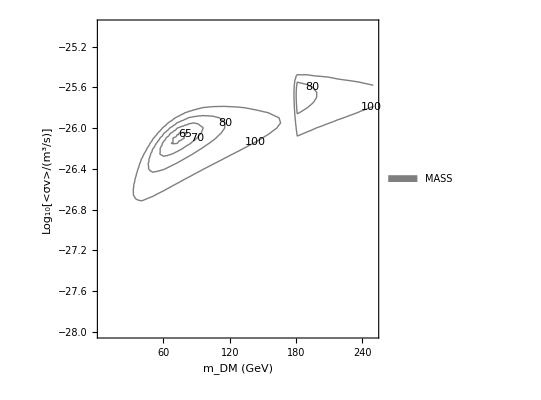

```mathematica
contdata01=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/contour_AMS_RED_mass01.dat","Table",HeaderLines->1];
contdata02=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/contour_AMS_RED_mass02.dat","Table",HeaderLines->1];
contdata03=Import["/Users/sinbi/mcirelli/Documents/mathematica/PPPC4DMID/three_mass/contour_AMS_RED_mass03.dat","Table",HeaderLines->1];
contdataLog01=Table[{contdata01[[i,1]],contdata01[[i,2]], contdata01[[i, 4]]},{i, Length[contdata01]}];
contdemoLog02=Table[{contdata02[[i,1]],contdata02[[i,2]], contdata02[[i, 4]]},{i, Length[contdata02]}];
contdataLog03=Table[{contdata03[[i,1]],contdata03[[i,2]], contdata03[[i, 4]]},{i, Length[contdata03]}];
ListContourPlot[contdataLog03,Contours-> {60, 65,70,80,100},
 FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,PlotLegends->Placed[SwatchLegend[{"MASS"},LegendMarkerSize->20],Right]]
```

```mathematica
10^2.4
```

251.189

```mathematica
Log[10, 173.0]
10^2.2
10^2.25
```

2.23805

158.489

177.828